## Prepare data

## Set up

```mathematica
alpha=2;
l=16;
hd="/Users/keitokiddo/VC_revision/Simulations/";
fl="2_16_GE";
wd=StringJoin[hd,fl];
SetDirectory[wd];
```

```mathematica
nrep=3;
nprop=13;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
wt=ConstantArray[0,l];
AA={"A","C"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"T"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"T"};
sequencesAA=StringJoin[#/.DigitToAARules]&/@sequences;
wtAA = sequencesAA[[1]];
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
MakeLapRec[alpha_,l_]:=Module[{L1,L,m},
L1 = SparseArray[alpha*IdentityMatrix[alpha] - ArrayReshape[ConstantArray[1,alpha^2],{alpha,alpha}]];
m=1;
L=L1;
While[m<l, L = KroneckerProduct[L, IdentityMatrix[alpha]] + KroneckerProduct[IdentityMatrix[alpha^m],L1];
m++];
L
]
L=MakeLapRec[alpha,l];//AbsoluteTiming
```

{8.2891,Null}

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

## *Functions

### Basic functions

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := If[Length@x<2, {}, Correlation[x, y]^2];


mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)MapPartialVal[list_,data_,height_]:=Module[{Ab},Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];Ab.data]
```

```mathematica
(*Krawtchouk polynomial*)
w[alpha_, k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[alpha,k,d],{d,0,l},{k,0,l}];
```

### Matrix coefficients

```mathematica
(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;
```

### Projection operators

```mathematica
Pby[x_,Pcoeffs_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
```

```mathematica
Pkby[x_,k_]:=Module[{Pcoeffs},Pcoeffs=Inverse[LPs].wkd[[All,k+1]];Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1]];
```

#### Export design matrix for glmnet

```mathematica
designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
```

```mathematica
(*varall = ConstantArray[0, alpha^l];
rules=Flatten[Table[Join[Table[designrules[sequences[[j]],k,wt,j],{k,3}]],{j,Length[sequences]}],2];
null3=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,0,3}]}];
Export["data/rules.tsv",Transpose@{Most[ArrayRules[null3]][[All,1]][[All,1]],Most[ArrayRules[null3]][[All,1]][[All,2]]},"TSV"];*)
```

### Build matrices

```mathematica
(*(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[Join[ParallelTable[{i,i}->l(A-1),{i,1,A^l}],Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]*)
```

```mathematica
(*AbsoluteTiming[L=MakeLaplacian[alpha,l];]*)
```

```mathematica
(*MakeAdj[A_,l_]:=SparseArray[Flatten[ParallelTable[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]*)
```

```mathematica
(*Adj=MakeAdj[alpha,l];//AbsoluteTiming*)
```

```mathematica
(*Adj = -(L - SparseArray[Flatten[Table[{i,i}->(alpha-1)*l,{i,1,alpha^l}],2]]);*)
```

```mathematica
(*null = Table[
   Join[s2dTaylor[sequences[[i]], 0, wt], 
    s2dTaylor[sequences[[i]], 1, wt]], {i, Length[sequences]}];//AbsoluteTiming*)
```

```mathematica
(*null2=SparseArray[Table[Join[s2dTaylor[seq,0,wt],s2dTaylor[seq,1,wt],s2dTaylor[seq,2,wt]],{seq,sequences}]];//AbsoluteTiming*)
```

```mathematica
designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},

  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
```

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,0, 1}]],{j,Length[sequences]}],2];//AbsoluteTiming
```

{9.40206,Null}

```mathematica
nullonehot=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*(alpha)^k,{k,0,1}]}];
```

## Simulation

```mathematica
wd=StringJoin[hd,fl];
SetDirectory[wd];
```

```mathematica
GetVC[f_]:=Nbysum@Table[Norm[Pkby[f,k]]^2,{k,l}]
```

### Well defined random field with exponential lambdas

```mathematica
b=1;
a=4.;
sig[x_]:=1/(1+Exp[-a (x-b)])
siginv[y_]:=-(1/a)*Log[1/y-1] + b
```

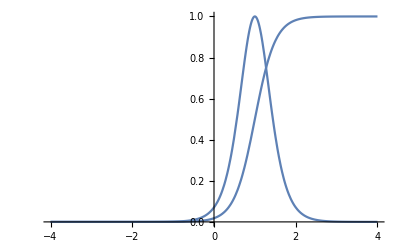

```mathematica
Show[Plot[sig[x],{x,-4,4}],
Plot[sig'[x],{x,-4,4},PlotRange->All]]
```

```mathematica
nrep=3;
```

```mathematica
(*VCExpected=PadRight[{0,.75,.25},l+1]//N;*)
```

```mathematica
VCExpected=Nbysum@PadRight[{.8,.2},l, 0]//N
```

{0.8,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

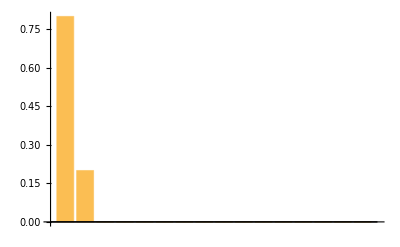

```mathematica
BarChart[VCExpected]
```

```mathematica
lambdas=VCExpected/Rest@mks
```

{0.05,0.00166667,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
phis=Table[{},nrep];
Do[
f=RandomVariate[NormalDistribution[],alpha^l];f=Table[Sqrt[(lambdas[[k]]mks[[k+1]]/Norm[Pkby[f,k]]^2)]Pkby[f,k],{k,1,l}]//Total;
phis[[i]]=f,
{i, nrep}]
```

```mathematica
(*Make WT sequence fittest*)
wtAAs=Table[sequences[[Position[phis[[i]],phis[[i]]//Max][[1,1]]]],{i,nrep}];
Do[phis[[i]]=phis[[i]][[seq2pos/@(Mod[#+wtAAs[[1]],2]&/@sequences)]],{i,nrep}]
Do[phis[[i]]=phis[[i]]/StandardDeviation[phis[[i]]],{i,Length@phis}]
Do[Export[StringJoin["data/",fl,"_phi_",ToString[i],".tsv"],phis[[i]],"TSV"],{i,nrep}]
```

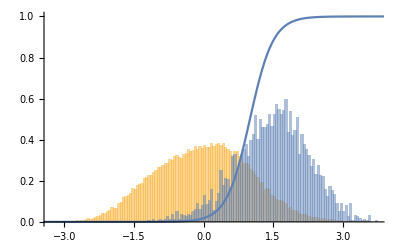

```mathematica
Show[
Histogram[{phis[[1]],phis[[1]][[trsmut[[2]]]]},100, "PDF"],
Plot[sig[x],{x,-4,4}]]
```

```mathematica
(*(*Add HOC component*)
Do[fs[[i]]=fs[[i]]+RandomVariate[NormalDistribution[0, Sqrt[2/3]*StandardDeviation[fs[[i]]]],alpha^l],{i,Length@fs}]*)
```

```mathematica
Do[fs[[i]]=sig/@phis[[i]],{i,nrep}]
Do[fs[[i]]=fs[[i]]/StandardDeviation[fs[[i]]],{i,nrep}]
Do[Export[StringJoin["data/",fl,"_f_",ToString[i],".tsv"],fs[[i]],"TSV"],{i,nrep}]
```

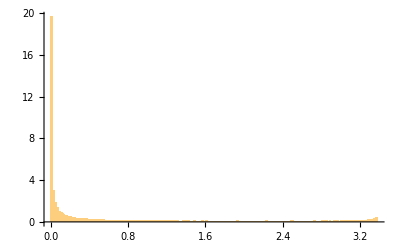

```mathematica
Histogram[fs[[1]],100,"PDF"]
```

```mathematica
VCtransformed=Nbysum@Table[Norm[Pkby[fs[[3]],k]]^2,{k,1,l}]
```

{0.544106,0.286863,0.099032,0.0243209,0.0209476,0.0138547,0.00633291,0.00267328,0.00120725,0.000481969,0.000137436,0.0000349896,6.69781×10^-6,1.07758×10^-6,1.48026×10^-7,3.58061×10^-9}

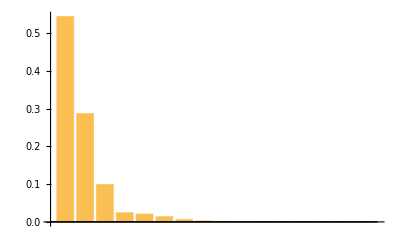

```mathematica
BarChart[VCtransformed]
```

```mathematica
lambdasTransformed=Table[Norm[Pkby[fs[[1]],k]]^2/mks[[k+1]],{k,1,l}]
```

{2213.28,156.353,9.17587,1.34653,0.392811,0.112105,0.0475047,0.0244178,0.0142084,0.0103621,0.00824495,0.00712343,0.00746465,0.00793188,0.00752567,0.0000887151}

```mathematica
SetDirectory[wd];
```

```mathematica
Export["data/lambdas.csv",PadLeft[lambdasTransformed,l+1]];
```

### Noised FL

```mathematica
noiseprops={.05, .1, .2, .3, .4, .5, .8};
```

```mathematica
varnoiselist = (1/(1-#) -1)&/@noiseprops * Variance[fs[[1]]//Flatten]
```

{0.0526316,0.111111,0.25,0.428571,0.666667,1.,4.}

```mathematica
noisevecslist = Table[RandomVariate[NormalDistribution[0, Sqrt[varnoiselist[[i]]]], alpha^l], nrep,{i,Length@noiseprops}];
```

```mathematica
fnlist=Table[fs[[j]]+noisevecslist[[j,i]], {j,nrep},{i,Length@noiseprops}];
```

```mathematica
Table[r2[fnlist[[1,i]], fs[[1]]],{i,Length@noiseprops}]
```

{0.949929,0.900472,0.799334,0.701436,0.600457,0.49742,0.199227}

```mathematica
Do[Export[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_", ToString[noiseprops[[j]]],".tsv"],fnlist[[i,j]],"TSV"],{i,nrep},{j,Length@noiseprops}]
```

```mathematica
Variance[fs[[1]]]
```

1.

### Experiment

```mathematica
(*fs=Table[{},nrep];
Do[
f=RandomVariate[NormalDistribution[],alpha^l];f=Table[Sqrt[(lambdas[[k]]mks[[k+1]]/Norm[Pkby[f,k]]^2)]Pkby[f,k],{k,1,l}]//Total;
fs[[i]]=f,
{i, nrep}]*)
```

```mathematica
(*Round[Table[Norm[Pkby[f,k]]^2/mks[[k+1]],{k,1,l}]-lambdas,10^7]
Do[fs[[i]]=fs[[i]]/StandardDeviation[fs[[i]]],{i,nrep}]*)
```

```mathematica
(*Histogram[fs[[1]],100,"PDF"]*)
```

```mathematica
b=1.;
a=2.;
sig[x_]:=1/(1+Exp[-a (x-b)])
```

```mathematica
sig[x_]:=x^2/(1+x^2)
```

```mathematica
(*sig[x_]:=8x^3 - 12x*)
```

```mathematica
(*sig[x_]:=x^5 - 10x^3 + 15x*)
```

```mathematica
(*sig[x_]:=x^4 - 6x^2+3*)
```

```mathematica
(*Plot[sig'[x],{x,-5,5},PlotRange->All]*)
```

```mathematica
(*Show[
Histogram[fs[[1]],100,"PDF"],
Plot[sig[x],{x,-5,5}, AspectRatio->1]
]*)
```

```mathematica
(*Do[fs[[i]]=sig/@fs[[i]],{i,nrep}]
Do[fs[[i]]=fs[[i]]/StandardDeviation[fs[[i]]],{i,nrep}]
(*Do[Export[StringJoin["data/",fl,"_f_",ToString[i],".tsv"],fs[[i]],"TSV"],{i,nrep}]*)*)
```

```mathematica
(*Histogram[fs[[1]],100,"PDF"]*)
```

```mathematica
(*VCtransformed=Nbysum@Table[Norm[Pkby[fs[[1]],k]]^2,{k,1,l}]*)
```

```mathematica
(*Mean@fs[[3]]*)
```

```mathematica
(*ListLogPlot[VCtransformed]*)
```

```mathematica
(*BarChart[VCtransformed]*)
```

```mathematica
(*BarChart[VCtransformed]*)
```

## Generate training samples

### Random sampling

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
trs=Table[RandomSample[Range[Length[sequences]],samplesizes[[i]]],{i,Length[samplesizes]}];
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
Do[Export[StringJoin[ "data/", "tr_",ToString[i],".tsv"],trs[[i]],"TSV"],{i,lg@trs}];
```

### Simulated mutagenesis

```mathematica
sequences[[Position[fs[[1]],fs[[1]]//Max][[1,1]]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
wt=ConstantArray[0,l];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
```

```mathematica
p=.1;
weights=(1-p)^(-#+l) p^# &/@hd;
```

```mathematica
(*Add all single mutant to top of training list*)
pos1d=seq2pos/@Table[ReplacePart[wt,p->1],{p,l}];
pos1d=Join[{1},pos1d];
```

```mathematica
trsmut=Table[RandomSample[weights->Range[alpha^l],Ceiling[i alpha^l]],{i,proportions}];
trsmut=Complement[#, pos1d]&/@trsmut;
trsmut=Table[Join[pos1d,trs],{trs,trsmut}];
```

```mathematica
tstmut=Table[Complement[Range[alpha^l],trsmut[[i]]]//Flatten,{i,Length[proportions]}];
```

```mathematica
(*proportion of sequences sampled*)
SortBy[hd[[trsmut[[1]]]]//Tally,First]
%[[All,2]]/mks[[;;Length[%]]]//N
```

{{0,1},{1,16},{2,120},{3,308},{4,160},{5,37},{6,12},{7,1}}

{1.,1.,1.,0.55,0.0879121,0.0084707,0.0014985,0.0000874126}

```mathematica
Do[Export[StringJoin["data/", "tr_mut_",ToString[i],".tsv"],trsmut[[i]],"TSV"],{i,lg@trsmut}];
```

## Export data to GE

```mathematica
geWD=StringJoin["/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/", fl];
SetDirectory[geWD];
```

#### Random

```mathematica
scheme="random";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"];
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fs[[i]][[trs[[j]]]], ConstantArray[0,trs[[j]]//Length], ConstantArray[fl, Length@trs[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],StringReplace["d = prepdata(dataf, :mut, :sequence, \"WT\", :f, cname = :condition, vname = :v)", "WT"->wtAA],"@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

#### Noised

```mathematica
scheme="noised";
```

```mathematica
name = StringJoin[fl, "_", scheme,"_"]
```

2_16_GE_noised_

```mathematica
J=3;
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trs[[j]]]], fnlist[[i,J]][[trs[[j]]]], ConstantArray[varnoiselist[[J]], Length@trs[[j]]], ConstantArray[fl, Length@trs[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,Length@trs}]
```

```mathematica
Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],StringReplace["d = prepdata(dataf, :mut, :sequence, \"WT\", :f, cname = :condition, vname = :v)", "WT"->wtAA],"@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]]},{i,nrep},{j,Length@trs}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},%]];
```

#### Mut

```mathematica
scheme="mut";
name = StringJoin[fl, "_", scheme,"_"];
```

```mathematica
Do[Export[StringJoin[name,ToString[i],"_",ToString[j],".txt"],Prepend[Transpose@{sequencesAA[[trsmut[[j]]]], fs[[i]][[trsmut[[j]]]], ConstantArray[0,Length@trsmut[[j]]], ConstantArray[fl, Length@trsmut[[j]]]},{"mut","f","v","condition"}],"CSV"],{i,nrep},{j,2}]
```

```mathematica
commands=Flatten@Table[{StringReplace["dataf = CSV.read(\"file\")","file"->StringJoin[name,ToString[i],"_",ToString[j],".txt"]],StringReplace["d = prepdata(dataf, :mut, :sequence, \"WT\", :f, cname = :condition, vname = :v)", "WT"->wtAA],"@time mlin = nonepistatic_model(d)","@time m = fit(mlin, nk = 4, tol = 1e-14)",StringReplace["writedlm(\"b_#.tsv\",m[:b])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"a_#.tsv\",m[:a])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],StringReplace["writedlm(\"yhat_#.tsv\",m[:yhat])","#"->StringJoin[name, ToString[i],"_",ToString[j]]],
" "},{i,nrep},{j,2}];
```

```mathematica
Export[StringJoin[name, "terminal.txt"],Join[{StringReplace["cd(\"#\")","#"->geWD],"using CSV","using DataFrames","using GlobalEpistasis"},commands]];
```

## Import GE results

```mathematica
deg=2; (*M-spline basis degree, I-spline degree is deg+1*)
elem=5; (*Number of splines in finished basis*)
knots=Range[0,1,1/(elem-deg)];
knots=Join[ConstantArray[knots[[1]],deg],knots,ConstantArray[knots[[-1]],deg]];
Table[Integrate[BSplineBasis[{deg,knots},i,x],x],{i,0,Length[knots]-deg-2}];
ReplacePart[%,
{{1,1,1,1}->BSplineBasis[{deg,knots},0,0]x,{-1,1}->Join[%[[-1,1]] ,{{(%[[-1]]/.x->1)+BSplineBasis[{deg,knots},Length[knots]-deg-2,1](x-1),x>1}}]}];
(basis=%/%[[All,2]]//Simplify);
transform[phi_,a_]:=First[a]+basis.Rest[a]/.{x->phi}
geprefix=fl;
geWD=StringJoin["/Users/keitokiddo/Dropbox (UFL)/VC_revision/GE/", fl];
SetDirectory[geWD];
schemes = {"random", "noised", "mut"};
names =StringJoin[fl, "_", #,"_"]&/@schemes;
```

```mathematica
pdsGE=Table[{},nschemes,nrep, Length[trs]];
```

```mathematica
Do[pdsGE[[k]][[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll, phige},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[l],AA}],{{geprefix}}],Thread[{Range[l],Characters[wtAA]}]];

FactorMatrix=Table[Join[{geprefix},Thread[{Range[l],Characters[sequencesAA[[k]]]}]],{k,trs[[j]][[;;Min[1000, Length@trs[[j]]]]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,alpha]&/@(Effects[[1;;]]/.AAtoDigitRules)) -alpha+1,b[[2;;]],alpha*l];
phige = nullonehot.Join[{b[[1]]},coeffsAll];
spline/@phige
],{k,1,1}, {i,nrep},{j,13}]
```

```mathematica
Do[pdsGE[[k]][[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll, phige},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[l],AA}],{{geprefix}}],Thread[{Range[l],Characters[wtAA]}]];

FactorMatrix=Table[Join[{geprefix},Thread[{Range[l],Characters[sequencesAA[[k]]]}]],{k,trs[[j]][[;;Min[1000, Length@trs[[j]]]]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,alpha]&/@(Effects[[1;;]]/.AAtoDigitRules)) -alpha+1,b[[2;;]],alpha*l];
phige = nullonehot.Join[{b[[1]]},coeffsAll];
spline/@phige
],{k,2,2}, {i,nrep},{j,13}]
```

```mathematica
Do[pdsGE[[k]][[i,j]]=Module[{y,b,a,yhat,spline,PossibleEffects,FactorMatrix,SortedEffects,Effects,coeffsAll, phige},
b=Transpose[Import[StringReplace["b_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
a=Transpose[Import[StringReplace["a_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
yhat=Transpose[Import[StringReplace["yhat_#.tsv","#"->StringJoin[names[[k]], ToString[i],"_",ToString[j]]]]]//Flatten;
spline[x_]:=transform[x,a];
PossibleEffects=Complement[Join[Tuples[{Range[l],AA}],{{geprefix}}],Thread[{Range[l],Characters[wtAA]}]];

FactorMatrix=Table[Join[{geprefix},Thread[{Range[l],Characters[sequencesAA[[k]]]}]],{k,trsmut[[j]]}];SortedEffects=SortBy[Transpose[{PossibleEffects,Table[Min[Position[Flatten[FactorMatrix,1],PossibleEffects[[i]]]],{i,Length[PossibleEffects]}]}],Last];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];Effects=Pick[SortedEffects[[All,1]],NumberQ/@SortedEffects[[All,2]]];coeffsAll=MapPartialVal[(FromDigits[#,alpha]&/@(Effects[[1;;]]/.AAtoDigitRules)) -alpha+1,b[[2;;]],alpha*l];
phige = nullonehot.Join[{b[[1]]},coeffsAll];
spline/@phige
],{k,3,3}, {i,nrep},{j,2,2}]
```

```mathematica
SetDirectory[StringJoin[wd]];
```

```mathematica
pdsGE>> "pdsGE.m";
```

```mathematica
(*pdsGE = Import[StringJoin[wd,"/pdsGE.m"]];*)
```

## Analysis

## Functions

```mathematica
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
```

```mathematica
nmodels=4;
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD];
SetDirectory[wd];
```

```mathematica
r2[x_, y_] := If[Length@x<2, {}, If[Variance[x]==0||Variance[y]==0,0, Correlation[x, y]^2]];
mse[x_, y_] := Mean[(x - y)^2];
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
w[alpha_,l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
```

## Plotting parameters

```mathematica
nrep=3;
nschemes=3;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

#### Colors

```mathematica
blue=RGBColor@@({5,112,176}/255);
lightblue=RGBColor@@({116,169,207}/255);
colors={GrayLevel[.7],RGBColor@@({116,196,118}/255),Lighter[lightblue,.2],Darker[blue,.2],Black}//Reverse;
```

#### Sizes

```mathematica
fontsize=19;
thickness=AbsoluteThickness[1.5];
pt=.2;
```

#### Styles

```mathematica
fstyle=Table[{GrayLevel[.3],AbsoluteThickness[1]},4];
```

```mathematica
style={#,thickness}&/@colors;
```

```mathematica
(*barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.2],"WhiskerStyle"->Black|>;*)
```

```mathematica
barstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.3]|>;
ebstyle=<|"FenceStyle"->{GrayLevel[.25], thickness},
"WhiskerStyle"->{GrayLevel[.25], thickness},
"FenceWidth"->Scaled[.4]|>;
(*Bar style - R2 plots*)
R2ErrorBarStyle={#,thickness}&/@colors;
```

#### Labels

```mathematica
modelnames={"VC regression","Three-way","Pairwise","Global epistasis","Additive"};
modellabs=Style[#,FontFamily->"Helvetica"]&/@modelnames;
```

## Plotting functions

```mathematica
errorplotdat[data_]:=Module[{means},
means=Mean@data;
Table[Around[means[[i]], {Quantile[data[[All,i]],.025]-means[[i]],Quantile[data[[All,i]],.975]-means[[i]]}],{i,Dimensions[data][[2]]}]
]
```

```mathematica
w[alpha_,l_,k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q] (*Krawtchouk polynomial*)
```

```mathematica
greekletter[l_]:=Style[l/.{Alpha->α, Beta->β, Gamma->γ, Rho->ρ, Lambda ->λ},FontFamily->"Stencil", FontSize->16]
```

```mathematica
summaryfig3[lambdas_,lambdaspos_, vcs_,  alpha_, l_]:=Module[
{},
wkd = Table[w[alpha,l, k,d],{d,0,l},{k,0,l}];
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
(*rho prior*)
rho = wkd[[All,2;;]].Rest[lambdas];
plotdat=Transpose@{Range[0,l],Nbyfirst[rho]};
figrho=Show[
ListLinePlot[
plotdat,
Frame->True,
FrameStyle->fstyle,
FrameLabel->{"Hamming Distance",ToString[ρ]},
FrameTicks->{{Range[-1,1,.2]/.{1.->1,0.->0},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
PlotStyle->{GrayLevel[.5], thickness},
BaseStyle->{FontSize->fontsize},
ImageSize->400,
AspectRatio->.75,
PlotRange->{{0,l+.2},{-.4,1}},
PlotRangeClipping->False
],
ListPlot[
plotdat,
PlotStyle->{Gray}
]
];
(*rho posterior*)
rhopos = Table[Nbyfirst[wkd[[All,2;;]].Rest[lambdaspos[[i]]]],{i,Length[lambdaspos]}];
plotdat=errorplotdat[rhopos];
figrhopos = Show[
ListPlot[
plotdat,DataRange->{0,l},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];(*vc prior*)
vc=Transpose@{Range[1,l],Nbysum[Rest@lambdas*Rest@multiplicities]};
figvcBar=BarChart[vc[[All,2]],ChartLabels->vc[[All,1]],
Frame->True,
FrameLabel->{"Interaction order","Variance explained"},
FrameTicks->{{Range[0,1,.1]/.{0.->0},None},{Range[1,l,1],None}},
FrameStyle->fstyle,
BaseStyle->{FontSize->fontsize},
ChartStyle->GrayLevel[.7],
ImageSize->400,
PlotRange->{{.5,l+.5},All},
PlotRangeClipping->False,
AspectRatio->.75
];
(*vc posterior*)
vcpos = Table[Nbysum[Rest@lambdaspos[[i]]*Rest@multiplicities],{i,Length[lambdaspos]}];
plotdat = errorplotdat[vcpos];
figvcpos = Show[
ListPlot[plotdat,DataRange->{1,l},PlotRange->{0,1},PlotStyle->{GrayLevel[.25],thickness},IntervalMarkersStyle->barstyle,Joined->False],
ListLinePlot[plotdat[[All,1]],DataRange->{1,l},PlotRange->{0,1},PlotStyle->{GrayLevel[.25],thickness}]];
(*Gamma Prior*)
ck = Table[Table[2^k (-1)^q Binomial[k,q],{q,0,l}],{k,0,l}];
mk=Table[Table[PadLeft[ck[[k]],l+d][[;;l+1]],{d,1,l+1}],{k,l+1}];
gammak=Table[(mk[[k]].wkd.lambdas),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
gammak=Table[(mk[[k]].rho),{k,Length[mk]}];
gammak=Table[gammak[[k+1]][[;;l+1-k]],{k,0,l}];
k=1;
figgamma=Table[
Module[{plotdat},
plotdat=Transpose@{Range[0,Length[gammak[[k+1]]]-1],Nbyfirst[gammak[[k+1]]]};
Show[
ListLinePlot[
plotdat,
Frame->True,
FrameLabel->{"Hamming Distance",Subscript[greekletter[Gamma],ToString[k]]},
FrameTicks->{{Range[0,2,.2]/.{0.->0,1.->1},None},{Range[0,l,1]/.{0.->0},None}},
Axes->True,
AxesStyle->Directive[Gray,Dashed],
BaseStyle->{FontSize->fontsize},
PlotStyle->{GrayLevel[.5], thickness},
ImageSize->400,
AspectRatio->.75,
FrameStyle->fstyle,
PlotRange->{{0,l+.2},{-.12,1}},
PlotRangeClipping->False],
ListPlot[
plotdat,
PlotStyle->{Gray}]]
],{k,0,3}];
(*Gamma posterior*)
gamma1pos=Table[Most[mk[[2]].rhopos[[i]]],{i,Length[rhopos]}];
gamma1pos = Nbyfirst/@gamma1pos;
plotdat = errorplotdat[gamma1pos];
figgamma1pos = Show[
ListPlot[plotdat,DataRange->{0,l-1},PlotStyle->{GrayLevel[.25]},IntervalMarkersStyle->barstyle,Joined->False,PlotRange->All],
ListLinePlot[Join[{1},plotdat[[2;;,1]]],DataRange->{0,l-1},PlotRange->All,PlotStyle->{GrayLevel[.25], thickness}]];
{Show[figrho,figrhopos],Show[figvcBar,figvcpos],Show[figgamma[[2]],figgamma1pos]}
]
```

```mathematica
MakeR2figure[input_]:=Module[
{r2s,r2snoised},
r2s=input[[1]][[{1,4,3,2}]];
r2snoised=input[[2,2]][[{1,4,3,2}]];
plotdatError=Table[Table[{Around[proportions[[i]],0],Around[Mean[r2s[[k,All,i]]],StandardDeviation[r2s[[k,All,i]]]]},{i,Length[proportions]}],{k,Length[r2s]}];
plotdatLine=Table[Table[{proportions[[i]],Mean[r2s[[k,All,i]]]},{i,Length[proportions]}],{k,Length[r2s]}];
figR2Line=ListPlot[
plotdatLine,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
PlotStyle->style,
FrameStyle->fstyle,
FrameTicks->{{Range[.1,1,.1]/.{1.->1},False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,
AxesOrigin->{0,.8},
AxesStyle->Directive[Transparent,Dashed]];
figR2Error=ListPlot[
plotdatError,
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
IntervalMarkersStyle->R2ErrorBarStyle,
PlotStyle->style,
FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},
Joined->False,
PlotRangeClipping->False,
ImageSize->400];
plotdat2=Table[Table[{Around[proportions[[i]],0],Around[Mean[r2snoised[[k,All,i]]],StandardDeviation[r2snoised[[k,All,i]]]]},{i,Length[proportions]}],{k,Length[r2s]}];figNoiseR2tr=
ListPlot[
plotdat2,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
Frame->True,
IntervalMarkersStyle->R2ErrorBarStyle,
PlotStyle->Table[Join[style[[i]],{Dashed}],{i,nmodels}],
FrameStyle->fstyle,
FrameTicks->{{Range[.1,1,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Reconstruction "Superscript[R,2]},
Joined->True,
ClippingStyle->None,
ImageSize->400(*PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],{.75,.25}],*)
];
Show[figR2Line,figR2Error,figNoiseR2tr]
]
```

```mathematica
MSErecon[mselist_,fl_]:=Module[
(*input is table of mse, dim=nmodels x nrep x nprop*)
{},
fs=Table[{},nrep];Do[fs[[i]]=Import[StringJoin[HD,fl, "/data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
input=mselist[[{1,4,3,2}]];
input=input/(.2*Variance[fs[[1]]]);plotdat=Table[Table[{Around[proportions[[j]],0],Around[Mean[input[[k]][[All,j]]],StandardDeviation[input[[k]][[All,j]]]]},{j,Length[proportions]}],{k,nmodels}];
Show[ListLogPlot[
plotdat,
AxesStyle->Directive[Gray,Dashed],
AxesOrigin->{0,1},
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
PlotRange->{{0,1},{.1, 8}},
Frame->True,
PlotStyle->style,
IntervalMarkersStyle->R2ErrorBarStyle,
FrameStyle->fstyle,
FrameTicks->{{{0.05, 0.1, 0.5, 1, 5, 10},False},{{0,.2,.4,.6,.8,1},False}},
FrameLabel->{"Proportion training data","Reconstruction MSE"},
Joined->True,
PlotRangeClipping->False,
ImageSize->400]]
]
```

```mathematica
legpos={.3,.75};
MSEbyD[results_,fl_, trmut_, alpha_,l_, sampling_]:=Module[
{input,ylim},
fs=Table[{},nrep];Do[fs[[i]]=Import[StringJoin[HD,fl, "/data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];input=results[[{1,4,3,2}]];
ylim=10;
yticks=Range[1,ylim, 1];
A=Range[0,alpha-1];
sequences=Tuples[A,l];
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
ttmut=Complement[Range[alpha^l],trmut];
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];proportions=samplesizes/(alpha^l);
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[ttmut,seqbyhd[[d]]], {d, l+1}];lgs=Length/@tstbyD;
trsdensity = 1-lgs/mks;
dmin=First[Position[#=={}&/@tstbyD,False][[1]]] -1;
plotdat=Table[{Around[d,0],Around[Mean[input[[k]][[d+1]]/Variance@fs[[1]]],
.5StandardDeviation[input[[k]][[d+1]]/Variance@fs[[1]]]]},{k,nmodels},{d,dmin,l}];
plotsampling=ListPlot[trsdensity,
BaseStyle->{FontSize->fontsize},
DataRange->{0,l},
PlotRange->{{0,l+.2},{0,1}},
Frame->True,
PlotStyle->{GrayLevel[0],Thickness[0.004],PointSize[0.02]},
FrameStyle->fstyle,
FrameTicks->{{Automatic,False},{Range[0,l],False}},FrameLabel->{"Distance to WT","Sampling density"},
PlotRangeClipping->False,
AspectRatio->.75,
ImageSize->400,
AxesStyle->Directive[Gray,Dashed],
AxesOrigin->{0,1}
];
plotr2d=Show[ListLogPlot[
plotdat,
BaseStyle->{FontSize->fontsize},
AspectRatio->1,
(*Adjust Plot Range*)
PlotRange->{{0,l+.2},{.007, 100}},
Frame->True,
PlotStyle->style,
IntervalMarkersStyle->R2ErrorBarStyle,
FrameStyle->fstyle,
FrameTicks->{{Automatic,False},{Range[0,l],False}},FrameLabel->{"Hamming Distance to WT","Scaled out-of-sample MSE"},
Joined->True,
PlotRangeClipping->False,
ImageSize->400,PlotLegends->Placed[LineLegend[Automatic,modellabs,LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendMargins->0],legpos],
AxesStyle->Directive[Gray,Dashed],
AxesOrigin->{0,1}
]];
{plotsampling,plotr2d}
]
```

```mathematica
Make6P[i_]:=Module[
{},
lambdaspos=Import[StringJoin[fls[[i]], "/out/", "posterior_lambdas.csv"]];
If[Length@lambdaspos==0,
lambdaspos=PadLeft[#,ls[[i]]+1]&/@Table[lambdasAll[[i]]+RandomVariate[NormalDistribution[0,.001],ls[[i]]],10]];
panels=Join[summaryfig3[PadLeft[lambdasAll[[i]],ls[[i]]+1],lambdaspos,vcsAll[[i]],  alphas[[i]], ls[[i]]], {MakeR2figure[results[[i]][[1]]],MSErecon[results[[i,2,2,1]],fls[[i]]],MSEbyD[results[[i]][[2,3]],fls[[i]],trmutAll[[i]], alphas[[i]],ls[[i]], samplings[[i]]][[2]]}];
Labeled[Grid[ArrayReshape[labelfigs[panels],{3,2}],Spacings->{1,.5}],panlabs[[i]],{{Top,Center}},Spacings->{0,2}]
]
```

```mathematica
labelfigs[figs_]:=Table[
Show[figs[[i]], Epilog->Text[Style[FromCharacterCode[64+i],Bold,FontFamily->"Helvetica", FontSize->fontsize+2],ImageScaled@{0.02,.95}],ImagePadding->{{65,5},{60,10}}],
{i,Length[figs]}
]
```

```mathematica
labelfigs[fig_,lab_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->{{80,5},{60,20}}]
```

```mathematica
labelfigspad[fig_,lab_,pad_]:=Show[fig, Epilog->Text[Style[lab,Bold,FontFamily->"Helvetica", FontSize->fontsize],ImageScaled@{.04,.95}],ImagePadding->pad]
```

## Processing

```mathematica
nrep=3;
```

```mathematica
alpha=2;(* alleles per site *)
l=16;(* length of sequence *)
fl="2_16_GE";
```

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];
```

```mathematica
R2s=Table[{},nschemes];
MSEs=Table[{},nschemes];
```

### Import FL

```mathematica
fs=Table[{},nrep];
Do[fs[[i]]=Import[StringJoin["data/",fl,  "_f_", ToString[i],".tsv"]]//Flatten,{i,nrep}];
fns=Table[{},nrep];
Do[fns[[i]]=Import[StringJoin["data/",fl,  "_f_","noised_", ToString[i],"_","0.2",".tsv"]]//Flatten,{i,nrep}];
```

### Import training samples

```mathematica
trs=Table[{},Length@proportions];
Do[trs[[i]]=Import[StringJoin["data/", "tr_",ToString[i],".tsv"]]//Flatten,{i,Length@proportions}]
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

```mathematica
trsmut=Table[{},Length@proportions];
Do[trsmut[[i]]=Import[StringJoin["data/", "tr_mut_",ToString[i],".tsv"]]//Flatten,{i,Length@trsmut}]
ttsmut=Table[Complement[Range[alpha^l],trsmut[[i]]],{i,Length[trsmut]}];
```

### Import GE results

```mathematica
pdsGE = Import["pdsGE.m"];
```

### Import glmnet results

#### 2way

```mathematica
pds2way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="2way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds2way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

#### 3way

```mathematica
pds3way=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="3way";
```

```mathematica
Do[
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"];
pds3way[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

### Import VC results

```mathematica
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pdsVC=Table[{}, nschemes, nrep, Length@proportions];
```

```mathematica
modelname="vc";
```

```mathematica
Do[
If[schemes[[k]]=="noised", name=StringRiffle[{fl, schemes[[k]], modelname, i, "0.2", j}, "_"], 
name=StringRiffle[{fl, schemes[[k]], modelname, i, j}, "_"]];
pdsVC[[k,i,j]]=Import[StringJoin["out/", name,".tsv"]]//Flatten,
{k,nschemes},{i,nrep}, {j,Length@proportions}
]
```

Import::nffil: File out/2_16_GE_mut_vc_1_4.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_GE_mut_vc_1_5.tsv not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File out/2_16_GE_mut_vc_1_6.tsv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

### Calculate

```mathematica
pdsAll={pdsVC, pdsGE, pds2way,pds3way};
nmodels=Length[pdsAll];
```

#### Random

```mathematica
pds=pdsAll[[All, 1]];
R2s[[1]]=Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
MSEs[[1]]=Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}];
```

#### Noise

```mathematica
pds=pdsAll[[All,2]];
R2s[[2]]={Table[r2[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[r2[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
MSEs[[2]]={Table[mse[pds[[k]][[i,j]][[trs[[j]]]],fs[[i]][[trs[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}],
Table[mse[pds[[k]][[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{k,nmodels}, {i,nrep},{j,Length[proportions]}]};
```

```mathematica
MSEs[[2]]//Dimensions
```

{2,4,3,13}

#### Mut

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD,fl];
SetDirectory[wd];
```

```mathematica
pds=pdsAll[[All,3]];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,Length@seqsbyD}];j=2;tstbyD=Table[Intersection[tstmut[[j]],seqbyhd[[d]]], {d, l+1}];Length/@tstbyD;
 %/mks//N;
trsdensity = 1-%;
Position[#=={}&/@tstbyD,False][[1]]//First ;
dmin=%-1;
```

```mathematica
R2s[[3]]=Table[r2[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
MSEs[[3]]=Table[mse[fs[[i]][[tstbyD[[d]]]], pds[[k]][[i]][[j]][[tstbyD[[d]]]]],{k,nmodels},{d,l+1},{i,nrep}];
```

```mathematica
R2s[[1, 2,1,3]] = 0.71;
R2s[[2,2, 2]] = 0.723;
```

```mathematica
MSEs[[2,1,2]][[1,3]]=0.265;
```

```mathematica
result={R2s,MSEs};
```

### Export results

```mathematica
Export[StringJoin["../Results/Results_",fl,".m"], {R2s,MSEs}];
```

## Plotting

```mathematica
HD="/Users/keitokiddo/VC_revision/Simulations/";
wd=StringJoin[HD];
SetDirectory[wd];
```

```mathematica
nmodels=4;
nrep=3;
```

### Plot 2^16 GE

```mathematica
(*lambdaspos=Import[StringJoin[fl, "/out/", "posterior_lambdas.csv"]];*)
```

```mathematica
lambdaspos=Table[Import[StringJoin[fl, "/out/", "2_16_GE_random_lda_",ToString[i],"_10.tsv"]]//Flatten,{i,3}];
```

```mathematica
trmut=trsmut[[2]];
```

```mathematica
(*summaryfig3[PadLeft[lambdasTransformed,l+1],lambdaspos,VCtransformed,  alpha, l]*)
```

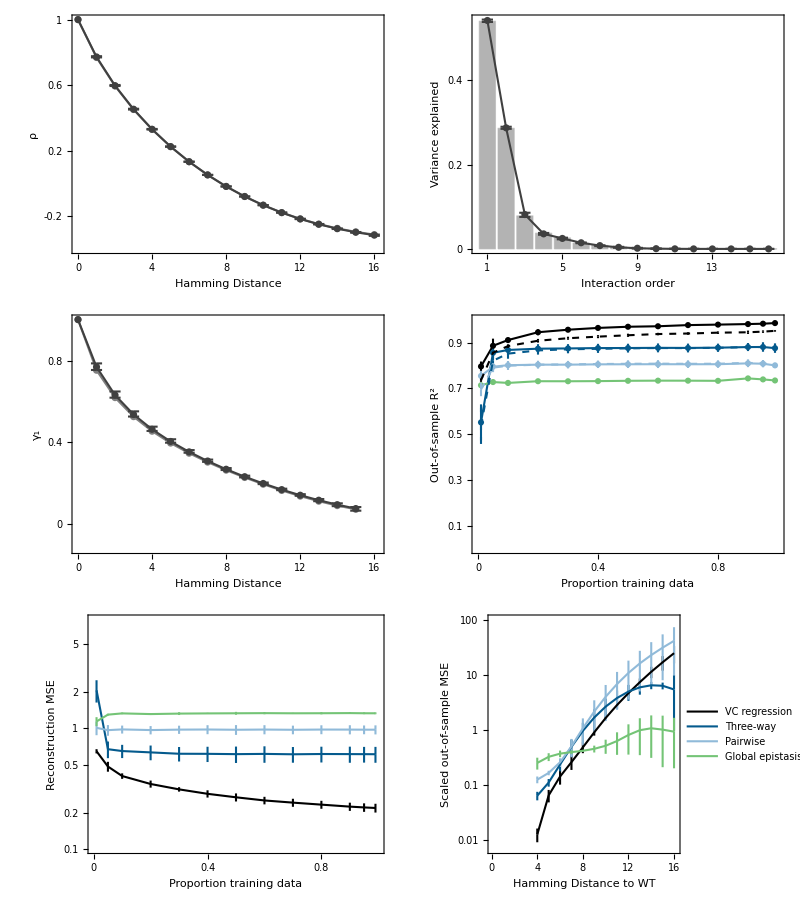

```mathematica
panels=Join[summaryfig3[PadLeft[lambdasTransformed,l+1],lambdaspos,VCtransformed,  alpha, l], {MakeR2figure[result[[1]]],MSErecon[result[[2,2,1]],fl],MSEbyD[result[[2,3]],fl,trmut, alpha,l, ""][[2]]}];
Grid[ArrayReshape[labelfigs[panels],{3,2}],Spacings->{1,.1}]
Export[StringJoin["2_16_GE.pdf"], %];
```

```mathematica
Directory[]
```

/Users/keitokiddo/VC_revision/Simulations/2_16_GE